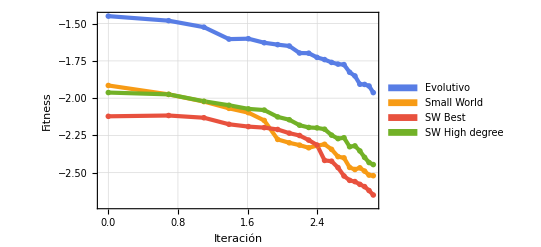

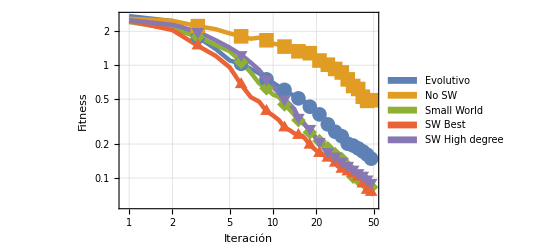

```mathematica
evolutivo = {2.720367192,2.463013718,1.77159349,1.389624966,1.100233163,1.027983416,0.924365046,0.846552799,0.749138833,0.698870263,0.644354327,0.604489266,0.566165561,0.533205465,0.507781597,0.481091639,0.468428676,0.428372817,0.420980226,0.386019477,0.366276682,0.341628938,0.334838903,0.298796063,0.266226851,0.259109636,0.256985605,0.25476331,0.247606831,0.234670537,0.227594883,0.217936793,0.201135853,0.201688931,0.196287689,0.193796443,0.19203103,0.183199554,0.182992858,0.177928503,0.175303771,0.172029798,0.17006777,0.169493148,0.160995464,0.157097687,0.148588298,0.148398503,0.146840314,0.140478911};
nosw = {2.57943963,2.474301716,2.218701418,2.081384451,1.910165465,1.800672649,1.71527211,1.752145957,1.662110312,1.553851119,1.515897726,1.460587546,1.432406188,1.385482847,1.325947408,1.301912494,1.297168205,1.276476386,1.204301615,1.1561373,1.098955053,1.064075791,1.022196091,1.009877783,0.9678431,0.930444792,0.926570163,0.926906707,0.91263917,0.861443607,0.812682747,0.736443512,0.748206754,0.715533896,0.660785935,0.653685464,0.667269016,0.635257996,0.615431691,0.589546204,0.543390045,0.525417271,0.528827056,0.503292387,0.482632101,0.496226498,0.491425953,0.488638156,0.463705299,0.440201595};
sw={2.408892258,2.102029133,1.781135801,1.506981243,1.328819496,1.067124993,0.86030979,0.690458578,0.622722561,0.54787927,0.522186658,0.44836526,0.404998937,0.364998505,0.325517238,0.30723351,0.288675168,0.253722052,0.244433167,0.223944787,0.212291545,0.202523646,0.197751564,0.183512612,0.173573103,0.163960368,0.162650203,0.155820377,0.151110263,0.147362422,0.138821491,0.132280351,0.126402384,0.122782634,0.116513945,0.102610421,0.100307313,0.098752435,0.097011353,0.098409471,0.099311612,0.095998922,0.09142057,0.090664378,0.085037545,0.083854506,0.084814056,0.082956773,0.08076168,0.080440911};
swbest = {2.471406017,2.045417643,1.485644251,1.206793539,0.955867466,0.674121921,0.52069299,0.47474498,0.390314502,0.357774298,0.325483376,0.278802094,0.266054609,0.249140849,0.239184583,0.23624779,0.217110667,0.195898897,0.18511733,0.174550793,0.165529908,0.162827595,0.155667218,0.150314664,0.146812985,0.142489933,0.135771045,0.128011659,0.123746413,0.119817646,0.12046098,0.118671337,0.113589415,0.111820253,0.111056943,0.109683713,0.106994357,0.105342726,0.102145789,0.098799065,0.089119963,0.088663749,0.084925582,0.080282901,0.077967497,0.077321858,0.075893735,0.074753702,0.072820903,0.070665037};
swhd ={2.506084498,2.275593372,1.982437258,1.660993017,1.429660845,1.236611713,1.054006362,0.908401419,0.748929854,0.641076552,0.56148304,0.499501189,0.451560325,0.411090295,0.343963306,0.319462656,0.285719799,0.274051673,0.240215455,0.22564476,0.210090314,0.19846421,0.178413489,0.170975717,0.165209196,0.164417907,0.156045283,0.152506968,0.148657476,0.140518596,0.138829341,0.132529096,0.129047554,0.125934959,0.124945845,0.119342747,0.117086088,0.112865178,0.111179595,0.110872316,0.109891139,0.105611973,0.103138759,0.103784213,0.097696001,0.098260151,0.094982826,0.090963565,0.087865572,0.086664022};

ListLogLogPlot[{evolutivo[[30;;50]],sw[[30;;50]],swbest[[30;;50]],swhd[[30;;50]]},Joined->True,PlotRange->Full, GridLines->Automatic, FrameTicksStyle->Directive[Black,15],Frame->{{True,False},{True,False}},FrameLabel->{Style["Iteración",Black,Large],Style["Fitness",Black,Large]},PlotLegends->SwatchLegend[{"Evolutivo","Small World","SW Best","SW High degree"}], PlotTheme->"Business"]

ListLogLogPlot[{evolutivo,nosw,sw,swbest,swhd},Joined->True,PlotRange->Full,GridLines->Automatic, FrameTicksStyle->Directive[Black,15], Frame->{{True,False},{True,False}},FrameLabel->{Style["Iteración",Black,Large],Style["Fitness",Black,Large]},PlotLegends->SwatchLegend[{"Evolutivo","No SW","Small World","SW Best","SW High degree"}],Mesh->{Range[0,50,3]},PlotMarkers->{Automatic,15},PlotStyle->{Thickness[0.008]}]
```